# Final Project Plots

## Caleb Powell

## Theoretical Equations

```mathematica
Clear[λ,μ]
P0[ρ_]:=(1-ρ)/(1-ρ^11) (*Stationary Distribution*)
P[ρ_,n_]:=P0[ρ]*ρ^n (*Prob of being in state n*)
PBlock[ρ_]:=P[ρ,10](*Blocking Probability*)
L[ρ_]:=∑_(n=0)^10 n*P[ρ,n](*AVG num of Customers*)
B[ρ_]:= 1-P0[ρ](*AVG num of Cust being Served*)
Lq[ρ_]:=(L[ρ]-B[ρ] )(*Avergae Que Length*)
S[ρ_,λ_]:=L[ρ]/λ(*AVG sojourn time*)
S2[ρ_,μ_]:=1/(2μ)*(1-11 ρ^10+10 ρ^11)/((1-ρ)(1-ρ^11))(*AVG sojourn time in terms of μ*)
```

## Strategy 1

### Blocking Probability

#### λ Plot (Set μ = 0.5) (λ → {0,1} )

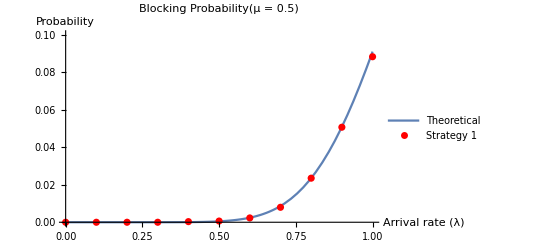

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*λ=0*)
S1y[[2]]=Mean[{0}];(*λ=0.1*)
S1y[[3]]=Mean[{0}];(*λ=0.2*)
S1y[[4]]=Mean[{0}];(*λ=0.3*)
S1y[[5]]=Mean[{0.00020000,0.00080000,0.00010000,0.00070000,0.00040000,0.00010000,0.00010000,0.00030000,0.00030000,0.00030000}];(*λ=0.4*)
S1y[[6]]=Mean[{0.00040000,0.00080000,0.00060000,0.00130000,0.00050000,0.00050000,0.00040000,0.00110000,0.00060000,0.00020000}]; (*λ=0.5*)
S1y[[7]]=Mean[{0.00290000,0.00280000,0.00270000,0.00070000,0.00150000,0.00170000,0.00320000,0.00210000,0.00210000,0.00330000}]; (*λ=0.6*)
S1y[[8]]=Mean[{0.00570000,0.01010000,0.00620000,0.00840000,0.01080000,0.00860000,0.00470000,0.00860000,0.01050000,0.00610000}]; (*λ=0.7*)
S1y[[9]]=Mean[{0.02390000,0.02260000,0.02280000,0.02410000,0.02550000,0.02280000,0.02290000,0.02660000,0.02300000,0.02060000}]; (*λ=0.8*)
S1y[[10]]=Mean[{0.04710000,0.05100000,0.06320000,0.04000000,0.04990000,0.04160000,0.05090000,0.05300000,0.05440000,0.05520000}]; (*λ=0.9*)
S1y[[11]]=Mean[{0.09290000,0.07630000,0.08790000,0.08740000,0.07350000,0.09100000,0.09790000,0.09500000,0.09050000,0.08940000}];(*λ=1.0*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
PBlock[λ/(2(0.5))],{λ,0,1},
PlotRange->{0,0.1},
AxesLabel->{"Arrival rate (λ)","Probability"},
PlotLabel->"Blocking Probability(μ  = 0.5)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### μ Plot (Set λ = 10) (μ → {0.5,6} )

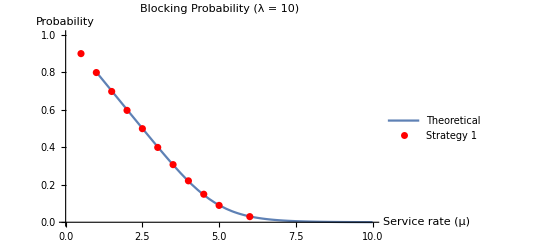

```mathematica
S1x = {0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,6};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0.89340000,0.89840000,0.90050000,0.89840000,0.89730000,0.90330000,0.89780000,0.90120000,0.90160000,0.89210000}]; 
S1y[[2]]=Mean[{0.79090000,0.80610000,0.79740000,0.79780000,0.79370000,0.80390000,0.79340000,0.79610000,0.80300000,0.79340000}];
S1y[[3]]=Mean[{0.70010000,0.69550000,0.69700000,0.70010000,0.69810000,0.70340000,0.69400000,0.69300000,0.69060000,0.69570000}];
S1y[[4]]=Mean[{0.58350000,0.60250000,0.59480000,0.59020000,0.59500000,0.60740000,0.59290000,0.60750000,0.59360000,0.59230000}];
S1y[[5]]=Mean[{0.49120000,0.50370000,0.50230000,0.51560000,0.49380000,0.49930000,0.50710000,0.48130000,0.48940000,0.50200000}];
S1y[[6]]=Mean[{0.39520000,0.39260000,0.39740000,0.40660000,0.38220000,0.40860000,0.42120000,0.40580000,0.39240000,0.38440000}]; 
S1y[[7]]=Mean[{0.31170000,0.32380000,0.30620000,0.29020000,0.32560000,0.30300000,0.29470000,0.31220000,0.28720000,0.31520000}]; 
S1y[[8]]=Mean[{0.20730000,0.22950000,0.21860000,0.22050000,0.22240000,0.20870000,0.22440000,0.21580000,0.23680000,0.22300000}];
S1y[[9]]=Mean[{0.15170000,0.14340000,0.14500000,0.15350000,0.15010000,0.15890000,0.14210000,0.15590000,0.14070000,0.15150000}];
S1y[[10]]=Mean[{0.08610000,0.09320000,0.09310000,0.08640000,0.09520000,0.07560000,0.08980000,0.07960000,0.10660000,0.09150000}]; 
S1y[[11]]=Mean[{0.03090000,0.02910000,0.02990000,0.03450000,0.03400000,0.03080000,0.02120000,0.03270000,0.02980000,0.02630000}];

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
PBlock[10/(2μ)],{μ,1,10},
PlotRange->{0,1},
AxesLabel->{"Service rate (μ)","Probability"},
PlotLabel->"Blocking Probability (λ = 10)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### ρ Plot (Choose and λ,μ such that ρ → {0,1})

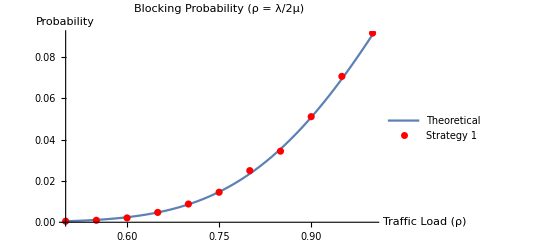

```mathematica
S1x = {0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0.00040000,0.00010000,0.00020000,0.00130000,0.00050000,0.00090000,0.00000000,0.00100000,0.00010000,0.00060000}]; 
S1y[[2]]=Mean[{0.00110000,0.00130000,0.00130000,0.00120000,0.00100000,0.00030000,0.00090000,0.00070000,0.00080000,0.00090000}];
S1y[[3]]=Mean[{0.00160000,0.00210000,0.00230000,0.00100000,0.00120000,0.00430000,0.00200000,0.00260000,0.00110000,0.00280000}];
S1y[[4]]=Mean[{0.00570000,0.00740000,0.00290000,0.00290000,0.00720000,0.00230000,0.00710000,0.00430000,0.00320000,0.00460000}];
S1y[[5]]=Mean[{0.00770000,0.01030000,0.00700000,0.01280000,0.01410000,0.00760000,0.00590000,0.00820000,0.00790000,0.00680000}];
S1y[[6]]=Mean[{0.01550000,0.01840000,0.01340000,0.01560000,0.01380000,0.01800000,0.01030000,0.01210000,0.01080000,0.01750000}];
S1y[[7]]=Mean[{0.02690000,0.02510000,0.02710000,0.03020000,0.02660000,0.02210000,0.02320000,0.02000000,0.02030000,0.02850000}]; 
S1y[[8]]=Mean[{0.04100000,0.03190000,0.02710000,0.03780000,0.03480000,0.03790000,0.03590000,0.03100000,0.03060000,0.03620000}];
S1y[[9]]=Mean[{0.05490000,0.05390000,0.04890000,0.05990000,0.05000000,0.04620000,0.04720000,0.05080000,0.04990000,0.04960000}]; 
S1y[[10]]=Mean[{0.08070000,0.06930000,0.06580000,0.06140000,0.05800000,0.07550000,0.07680000,0.07460000,0.07320000,0.07120000}];
S1y[[11]]=Mean[{0.08910000,0.08850000,0.08460000,0.09410000,0.09060000,0.10290000,0.08620000,0.09190000,0.09190000,0.09640000}];

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
PBlock[ρ],{ρ,0.5,1},
AxesLabel->{"Traffic Load (ρ)","Probability"},
PlotLabel->"Blocking Probability (ρ = λ/2μ)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

### Avg Queue Length

#### λ Plot (Set μ = 0.5) (λ → {0,1} )

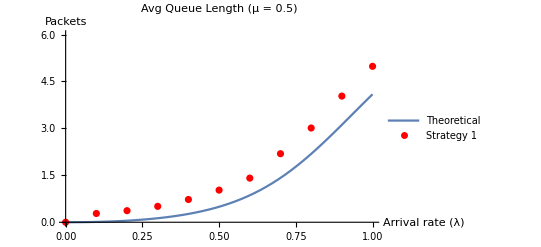

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*λ=0*)
S1y[[2]]=Mean[{0.27812155,0.27917982,0.28234235,0.28090437,0.27502422,0.28645980,0.27658120,0.28248534,0.27864799,0.28441944}];(*λ=0.1*)
S1y[[3]]=Mean[{0.37377244,0.37434106,0.36735607,0.37049987,0.36969532,0.37577329,0.37040802,0.36448019,0.37435922,0.35998759}];(*λ=0.2*)
S1y[[4]]=Mean[{0.51743916,0.50252138,0.50906737,0.50049042,0.49016755,0.52232179,0.49602856,0.50990367,0.50988298,0.52593151}];(*λ=0.3*)
S1y[[5]]=Mean[{0.73476267,0.69990102,0.75399391,0.73976738,0.72359324,0.72103923,0.70397074,0.71805659,0.71411848,0.76674931}];(*λ=0.4*)
S1y[[6]]=Mean[{1.01879753,1.01701309,1.04208395,1.01036931,0.98754096,1.03305731,1.14035776,1.02687181,0.97531187,1.02095626}]; (*λ=0.5*)
S1y[[7]]=Mean[{1.44743815,1.44860866,1.44407298,1.36778045,1.48151663,1.34187540,1.39496826,1.38280814,1.27519000,1.52493177}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.17281628,2.22497492,1.87851589,2.27955924,2.32348960,2.19455385,2.24494741,2.17282426,2.33799616,2.08365685}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.01138635,3.06190401,2.87510925,2.99500267,2.86024615,3.19179502,3.24316800,2.91313481,3.04060059,2.93322356}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.28144685,3.95490748,4.08620737,4.34640016,3.72486657,4.13716406,4.00421790,3.80950294,4.19516992,3.79053123}]; (*λ=0.9*)
S1y[[11]]=Mean[{4.97668359,5.16543192,4.98147021,4.59681840,5.05998187,4.77437066,5.36041912,4.83778264,4.84485931,5.24269465}];(*λ=1.0*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
Lq[λ/(2(0.5))],{λ,0,1},
PlotRange->{0,6},
AxesLabel->{"Arrival rate (λ)","Packets"},
PlotLabel->"Avg Queue Length (μ  = 0.5)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### μ Plot (Set λ = 2) (μ → {10,1} )

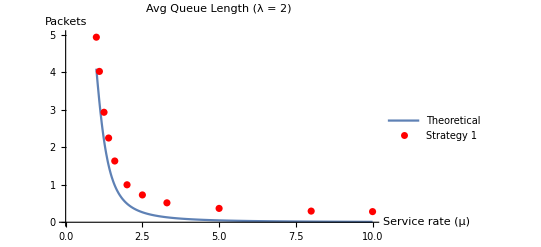

```mathematica
S1x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{5.15654684,4.64676863,5.11686747,4.89935683,4.86206061,5.04029537,5.13621760,4.80923353,4.92232986,4.70682343}]; (*μ=1*)
S1y[[2]]=Mean[{4.26765761,4.25699744,4.28892516,4.20443371,3.98112522,3.87089126,3.73844931,3.93255617,3.66781996,3.97195544}];(*μ=1.1*)
S1y[[3]]=Mean[{2.68651599,2.91022056,3.10376675,2.87670642,3.07882353,2.74220542,2.90016994,3.10172297,3.01156660,2.88654398}];(*μ=1.25*)
S1y[[4]]=Mean[{2.21765558,2.35530239,2.28311613,2.08258323,2.42580750,2.31424430,2.17626586,2.32942807,2.16329366,2.09253964}];(*μ=1.4*)
S1y[[5]]=Mean[{1.65615181,1.67112618,1.73244216,1.62104878,1.61497955,1.64538947,1.65410880,1.43843227,1.70073203,1.58076391}];(*μ=1.6*)
S1y[[6]]=Mean[{1.02609193,1.05548183,0.99667838,0.95671957,0.94410881,0.92881340,1.01741182,0.95252708,1.03245211,1.06848971}]; (*μ=2*)
S1y[[7]]=Mean[{0.69164342,0.74272352,0.74923060,0.75718299,0.74740726,0.73255343,0.72972596,0.72208835,0.67032940,0.73173235}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.53903193,0.48850577,0.49377528,0.51816052,0.51763212,0.50821747,0.52422711,0.53620359,0.52353680,0.52625844}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.38411495,0.37586180,0.36841073,0.37813917,0.37132228,0.36124597,0.35787286,0.36319304,0.35725613,0.37132985}]; (*μ=5*)
S1y[[10]]=Mean[{0.28974328,0.30233927,0.30195036,0.29824036,0.29860176,0.29564719,0.28727321,0.30087945,0.29487241,0.30378689}]; (*μ=8*)
S1y[[11]]=Mean[{0.28011530,0.27264588,0.28818681,0.28308032,0.28637158,0.28604515,0.28447798,0.28452140,0.28423670,0.28436819}];(*μ=10*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
Lq[2/(2μ)],{μ,1,10},
PlotRange->{0,5},
AxesLabel->{"Service rate (μ)","Packets"},
PlotLabel->"Avg Queue Length (λ = 2)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### ρ Plot (Choose and λ,μ such that ρ → {0,1})

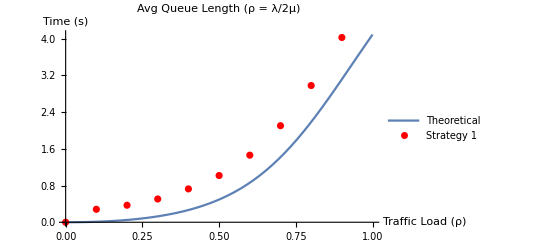

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*ρ=0*)
S1y[[2]]=Mean[{0.28579754,0.27933499,0.28478188,0.28777691,0.27257918,0.28272513,0.28550002,0.28772622,0.27034275,0.28740048}];
S1y[[3]]=Mean[{0.37353363,0.36807071,0.36880138,0.36424640,0.36725322,0.37607832,0.37159828,0.36708548,0.38179740,0.36925373}];
S1y[[4]]=Mean[{0.51342564,0.52682664,0.48531262,0.51191655,0.50527605,0.49740812,0.50771532,0.51312189,0.50622834,0.50479855}];
S1y[[5]]=Mean[{0.70714601,0.76840737,0.70695077,0.70303385,0.70254163,0.76369495,0.75893441,0.73191448,0.71972934,0.70681101}];
S1y[[6]]=Mean[{1.00877161,0.95402711,0.99557468,0.96557195,1.06391083,1.06181841,1.00823366,1.09347276,1.04849272,0.98246052}]; 
S1y[[7]]=Mean[{1.49197358,1.50444876,1.40476358,1.57591385,1.38684286,1.42156811,1.38468502,1.47979060,1.38554490,1.58462069}]; 
S1y[[8]]=Mean[{2.11764796,2.15772552,2.11440901,2.04488227,1.95182118,2.08741127,2.10909626,2.36357737,2.19884410,1.89823698}]; 
S1y[[9]]=Mean[{3.09343111,3.15381452,3.00159171,2.89268307,2.82872163,3.17657314,2.98595760,2.89459538,2.73421729,3.03456487}]; 
S1y[[10]]=Mean[{4.21180654,4.06706144,3.85755136,3.82799216,3.64510059,4.71004733,4.04350159,3.79401491,3.95113883,4.15780395}]; 
S1y[[11]]=Mean[{4.75776258,5.15535605,5.11737103,5.13354594,4.86994267,5.22045673,5.16799447,5.54861780,4.97547761,5.10090736}];

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
Lq[ρ],{ρ,0,1},
AxesLabel->{"Traffic Load (ρ)","Time (s)"},
PlotLabel->"Avg Queue Length (ρ = λ/2μ)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

### Avg Sojourn Time

#### λ Plot (Set μ = 0.5) (λ → {0,1} )

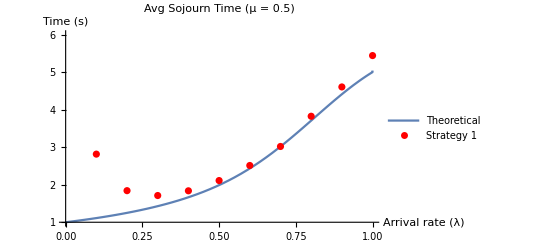

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{∞}]; (*λ=0*)
S1y[[2]]=Mean[{2.81358176,2.83475860,2.83207586,2.83291027,2.73862840,2.84147374,2.84258868,2.80004901,2.77923150,2.83119199}];(*λ=0.1*)
S1y[[3]]=Mean[{1.79935562,1.83643982,1.89169390,1.84523658,1.84604295,1.78515374,1.82535414,1.90006331,1.85848296,1.82715428}];(*λ=0.2*)
S1y[[4]]=Mean[{1.74189267,1.77278498,1.70198137,1.69297520,1.70137984,1.65396446,1.71999639,1.81834663,1.62005137,1.69623777}];(*λ=0.3*)
S1y[[5]]=Mean[{1.93578952,1.80708930,1.71258729,1.78679873,1.79012153,1.83269854,1.89686116,1.84274355,1.83322636,1.93842355}];(*λ=0.4*)
S1y[[6]]=Mean[{2.07704372,2.08629478,2.14490980,2.19565977,1.95867324,2.15082653,2.10361202,2.15939524,2.11644579,2.11367681}]; (*λ=0.5*)
S1y[[7]]=Mean[{2.32797589,2.38871560,2.64483769,2.36895260,2.67264764,2.67252411,2.52264919,2.72369338,2.35110069,2.44533339}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.78278393,2.91138933,3.14645367,3.00721159,3.11340963,3.25289972,3.10810542,2.91400409,2.74783930,3.19990098}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.79253325,3.82941603,3.52095384,3.96262679,3.92803821,3.82492114,3.82957452,3.84029596,3.63396139,4.07360015}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.68272912,4.71468203,4.29457237,4.49904664,4.71143118,4.35057620,4.82839938,4.85587240,4.70603549,4.40019867}]; (*λ=0.9*)
S1y[[11]]=Mean[{5.00694663,5.21161105,5.82765637,5.37998847,5.48824024,5.45233759,5.66345786,5.49111459,5.34533339,5.53350439}];(*λ=1.0*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S2[λ/(2(0.5)),0.5],{λ,0,1},
PlotRange->{1,6},
AxesLabel->{"Arrival rate (λ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (μ  = 0.5)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### μ Plot (Set λ = 2) (μ → {10,1} )

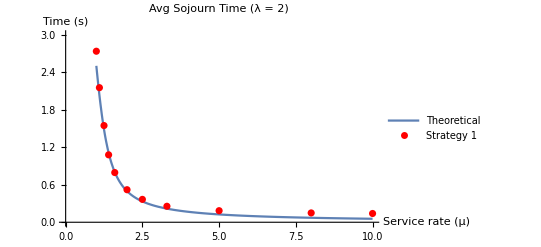

```mathematica
S1x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{2.47945363,2.87639322,2.61533687,2.74296000,2.59663451,2.86423400,2.81270753,2.63481124,2.77353385,2.93856173}]; (*μ=1*)
S1y[[2]]=Mean[{1.91427051,2.32821742,2.08951979,2.23466367,2.14155298,2.06456559,2.08516993,2.20123088,2.37264683,2.08008178}];(*μ=1.1*)
S1y[[3]]=Mean[{1.50902266,1.47657369,1.53018057,1.63632230,1.62214962,1.55433074,1.62551482,1.39018691,1.49267871,1.61671383}];(*μ=1.25*)
S1y[[4]]=Mean[{1.17196285,0.98168309,1.04566172,1.06843049,1.05897364,1.15079895,1.04361281,1.13152165,1.04665280,1.07709132}];(*μ=1.4*)
S1y[[5]]=Mean[{0.78380105,0.77689689,0.82865395,0.82181310,0.80788252,0.78340151,0.76923576,0.79497755,0.80933085,0.76781921}];(*μ=1.6*)
S1y[[6]]=Mean[{0.53716975,0.48688136,0.51007501,0.51453857,0.50781391,0.53097685,0.49874113,0.55953013,0.50831632,0.54575677}]; (*μ=2*)
S1y[[7]]=Mean[{0.35821047,0.37328502,0.35951389,0.37253318,0.37311616,0.36688632,0.37343511,0.34445226,0.37611168,0.35803461}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.25720168,0.25801602,0.25718670,0.24688769,0.25866247,0.26941833,0.25414277,0.24737005,0.25908743,0.24684418}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.19624340,0.18036522,0.18160159,0.18666127,0.18023727,0.18327461,0.18557650,0.18271133,0.18586738,0.18434164}]; (*μ=5*)
S1y[[10]]=Mean[{0.14806625,0.14846098,0.14697138,0.14629023,0.14950863,0.15012869,0.15063334,0.15190433,0.14577782,0.15332870}]; (*μ=8*)
S1y[[11]]=Mean[{0.13945912,0.14071287,0.14120501,0.14035143,0.14204008,0.13958869,0.13854743,0.14003991,0.13671653,0.14134506}];(*μ=10*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[2/(2μ),2],{μ,1,10},
PlotRange->{0,3},
AxesLabel->{"Service rate (μ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (λ = 2)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```

#### ρ Plot (Choose and λ,μ such that ρ → {0,1})

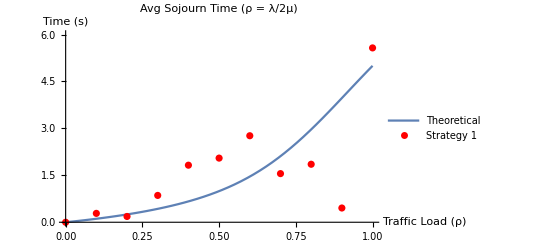

```mathematica
S1x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];

S1y[[1]]=Mean[{0}]; (*ρ=0*)
S1y[[2]]=Mean[{0.28877863,0.28468315,0.27838911,0.27861721,0.28868149,0.27727456,0.27777495,0.28767532,0.28745779,0.28936898}];(*ρ=0.1,λ=1.0,μ=5.0*)
S1y[[3]]=Mean[{0.18316606,0.18960587,0.18008322,0.18256329,0.18708501,0.17833909,0.18653338,0.18412281,0.18375039,0.19261620}];(*ρ=0.2,λ=2.0,μ=5.0*)
S1y[[4]]=Mean[{0.84377037,0.83288525,0.83296394,0.84470923,0.86415761,0.88460286,0.87510843,0.85731036,0.90052348,0.84331812}];(*ρ=0.3,λ=0.6,μ=1.0*)
S1y[[5]]=Mean[{1.71193007,1.85751954,1.81377732,1.87219738,1.85940253,1.80063840,1.82651986,1.80110280,1.83535229,1.85993115}];(*ρ=0.4,λ=0.4,μ=0.5*)
S1y[[6]]=Mean[{2.04330393,2.13998829,2.05135746,2.02834871,2.11079550,2.10136919,2.09753555,2.03163919,1.95088093,1.95041476}]; (*ρ=0.5,λ=0.5,μ=0.5*)
S1y[[7]]=Mean[{2.58821640,2.75727858,2.85055339,2.78292460,2.83166435,2.83459755,2.81812472,2.67784667,2.71156561,2.80210976}]; (*ρ=0.6,λ=2,μ=10/6*)
S1y[[8]]=Mean[{1.52001275,1.46701055,1.65812670,1.50252114,1.58295582,1.65498331,1.58776860,1.46853667,1.58061700,1.52620396}]; (*ρ=0.7,λ=1.4,μ=1*)
S1y[[9]]=Mean[{1.83731110,1.92225297,1.79923541,1.86168374,1.88247253,1.85940693,1.73935688,1.85854239,1.93450405,1.84474144}]; (*ρ=0.8,λ=1.6,μ=1.0*)
S1y[[10]]=Mean[{0.47020711,0.43907103,0.48322236,0.52463769,0.42037087,0.41299038,0.46774667,0.43499620,0.46866425,0.43156158}]; (*ρ=0.9,λ=9.0,μ=5.0*)
S1y[[11]]=Mean[{5.46899581,5.44736170,6.04656886,5.54199500,5.58759482,5.35455940,5.12974146,5.87255689,5.60205272,5.67859840}];(*ρ=1.0,λ=1.0,μ=0.5*)

S1Data = Transpose[{S1x,S1y}];

TheorPlot = Plot[
S[ρ,1],{ρ,0,1},
PlotRange->{0,6},
AxesLabel->{"Traffic Load (ρ)","Time (s)"},
PlotLabel->"Avg Sojourn Time (ρ = λ/2μ)",
PlotLegends->{"Theoretical"}
];

S1Plot = ListPlot[
S1Data ,
PlotStyle->Red,PlotLegends->{"Strategy 1"}
];


Show[{TheorPlot,S1Plot}]
```